```mathematica
Manipulate[
Module[{t,S,L,w,r1,r2,base,T,rectangular,annular},
(*size stuff*)
t=0.001;(*m*)
S=0.01;

(*rectangular*)
L:=length/1000;
w:=width/1000;

(*annular*)
r1=0.002;(*base radius*)
r2:=radius2/1000;(*fin radius*)

base=0.0025;

T:=500*Cosh[44.72*(L-x)]/Cosh[44.72*L];
(*rectangular:=Show[
Graphics3D[{
GrayLevel[0.5],Cuboid[{0,0,0},{base,w,2*S+t}],
RGBColor[0.08,0.51,1.],Cuboid[{base,0,S},{base+L,w,S+t}]
}],
Plot3D[t+S+10^-4,{x,base,base+L},{y,0,w},Mesh->None,ColorFunction->Function[{x,y,z},RGBColor[1,x,0]]]
];*)

rectangular:=Show[
Graphics3D[{
GrayLevel[0.5],Cuboid[{0,0,0},{base,w,2*S+t}],
(*RGBColor[0.08,0.51,1.],Cuboid[{base,0,S},{base+L,w,S+t}]*)
}],
RegionPlot3D[z<S+t,{x,base,base+L},{y,0,w},{z,S,S+t},Mesh->None,
ColorFunction->Function[{T,x,y},RGBColor[1,T,0]]
(*ColorFunction->Function[{T,x,y},RGBColor[1,Rescale[T,{350,500}],0]],ColorFunctionScaling->False*)
(*ColorFunction->Function[{T,L,y},ColorData[{"TemperatureMap","Reverse"}][T]]*)
(*ColorFunction->Function[{T,x,y},ColorData[{"TemperatureMap","Reverse"}][T]]*)
(*ColorFunction->(ColorData[{"TemperatureMap","Reverse"}][#1]&)*)
(*ColorFunction->Function[{T,x,y},RGBColor[1,Rescale[T,{350,500}],0]]*)
(*ColorFunction->Function[{x,y,z},RGBColor[1,x,0]]*)]
];

annular:=Graphics3D[{
GrayLevel[0.5],Cylinder[{{0,0,0},{0,0,2*S+t}},r1],
RGBColor[0.08,0.51,1.],Cylinder[{{0,0,S},{0,0,S+t}},r2]
}];

Show[Switch[fin,1,rectangular,2,annular],ViewPoint->{2,-2,1},Lighting->"Neutral",Boxed->False,ImageSize->{350,350}]
(*Table[{x,Rescale[T[x],{350,500}]},{x,0,L,0.001}]*)
],
Control[{{fin,1,""},{1->" rectangular ",2->" annular "},Setter}],
Style["fin measurements (mm)",Bold],
PaneSelector[{
1->Row[{
Control[{{length,10,"length"},5,20,1,Appearance->"Labeled",ImageSize->Small}],
Control[{{width,20,"width"},20,50,1,Appearance->"Labeled",ImageSize->Small}]
}],
2->Control[{{radius2,10,"radius"},5,15,1,Appearance->"Labeled",ImageSize->Small}]
},Dynamic@fin]
]
```

```mathematica
Manipulate[
Table[Graphics[{RGBColor[1,t,n*t],Disk[]}],{t,0,1,0.1}],
{n,0,1,0.1,Appearance->"Labeled"}]
```

```mathematica
Module[{f},
f:=Sin[x];
(*Plot3D[1,{x,0,4*π},{y,0,2*π},Mesh->None,ColorFunction->Function[{f,a,b},RGBColor[1,f,0]]]*)
(*Plot3D[1,{x,0,4*π},{y,0,2*π},Mesh->None,ColorFunction->Function[{x,y,z},RGBColor[1,Sin[x],0]]]*)
Plot3D[1,{x,0,4*π},{y,0,2*π},Mesh->None,ColorFunction->Function[{x,y,z},RGBColor[1,x,0]]]
]
```

-Graphics3D-

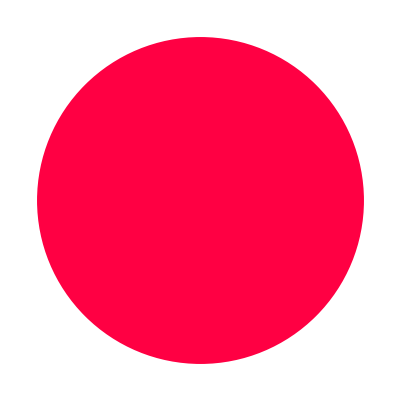



```mathematica
Graphics[{XYZColor[1,0,0],Disk[]}]
Graphics[{RGBColor[1,0,0],Disk[]}]
```

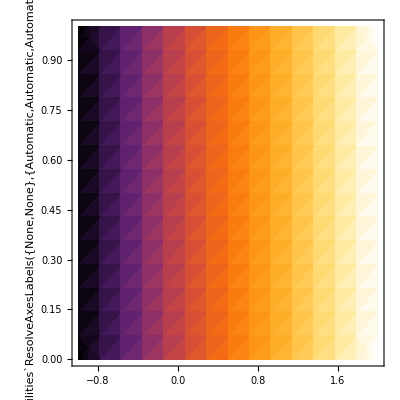
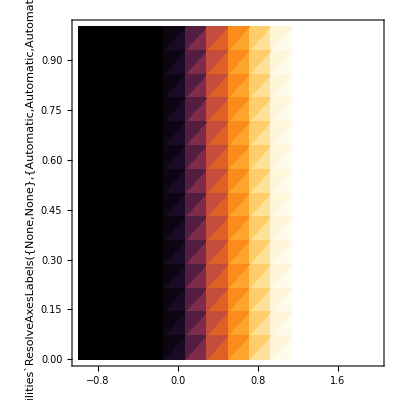

```mathematica
Table[DensityPlot[x,{x,-1,2},{y,0,1},ColorFunction->ColorData["SunsetColors"],ColorFunctionScaling->i],{i,{True,False}}]
```

```mathematica
Manipulate[
Module[{t,S,L,w,base,T,opt},
t=0.001;(*m*)
S=0.01;

L:=length/1000;
w:=width/1000;

base=0.0025;

T:=500*Cosh[44.72*(L-x)]/Cosh[44.72*L];

opt:=Sequence[Mesh->False,ViewPoint->{2,-2,1},Lighting->"Neutral",Boxed->False,ImageSize->400,PlotRange->{{base,base+L},{0,w},{0,2*S+t}},ImagePadding->20];

RegionPlot3D[z<S+t,{x,base,base+L},{y,0,w},{z,S,S+t},Evaluate@opt,
ColorFunction->Function[{T,x,y},RGBColor[1,T,0]]
]
],
Row[{
Control[{{length,10,"length"},5,20,1,Appearance->"Labeled",ImageSize->Small}],
Control[{{width,20,"width"},20,50,1,Appearance->"Labeled",ImageSize->Small}]}]
]
```